## Setup

NB!! Depending on whether we have inversion symmetry or not, where to put s changes

```mathematica
inversionSymmBroken = False;
If[inversionSymmBroken, tzsub=tz->tz, tzsub = tz->s tz] ;
```

```mathematica
ϵ[m_]:=If[m!=0,  tz kappa +Sign[m] α Sqrt[α Abs[m] + kappa^2],( tz- s α) kappa]/.α->1/.tzsub (* Keep α in the formula for later *)
```

```mathematica
alpha[m_]:=-Sqrt[Abs[m]]/((ϵ[m]- (tz/.tzsub) kappa)s- kappa)
```

```mathematica
xi=2*(HeavisideTheta[-ϵ[m]]-HeavisideTheta[-ϵ[n]])/((ϵ[m]-ϵ[n])^2 * (alpha[m]^2+1) *(alpha[n]^2+1));
```

```mathematica
stepRule[m_, n_]:=Switch[{m==0, n==0},
{True, True}, 0,
{False, False}, -1,
{True, False}, -HeavisideTheta[-kappa],
{False, True}, -HeavisideTheta[kappa]
] (* Assumes m > 0, n < 0 *)
```

NOTE : have to find out if the s before 2 kappa tz should be there

```mathematica
firstTerm[i_] =(ϵ[m] + ϵ[n]-0 2kappa (tz/.tzsub))alpha[i]^2 Switch[i, n, 1, m, -1]
```

(Abs[i] (If[m≠0,(s tz) kappa+Sign[m] √(1 Abs[m]+kappa^2),(s tz-s 1) kappa]+If[n≠0,(s tz) kappa+Sign[n] √(1 Abs[n]+kappa^2),(s tz-s 1) kappa]) Switch[i,n,1,m,-1])/(-kappa+s (-kappa s tz+If[i≠0,(s tz) kappa+Sign[i] √(1 Abs[i]+kappa^2),(s tz-s 1) kappa]))^2

```mathematica
secondTerm=Sqrt[Abs[n]]alpha[n] +Sqrt[Abs[n]-1]alpha[m]alpha[n]^2
```

-((√Abs[m] √(-1+Abs[n]) Abs[n])/((-kappa+s (-kappa s tz+If[m≠0,(s tz) kappa+Sign[m] √(1 Abs[m]+kappa^2),(s tz-s 1) kappa])) (-kappa+s (-kappa s tz+If[n≠0,(s tz) kappa+Sign[n] √(1 Abs[n]+kappa^2),(s tz-s 1) kappa]))^2))-Abs[n]/(-kappa+s (-kappa s tz+If[n≠0,(s tz) kappa+Sign[n] √(1 Abs[n]+kappa^2),(s tz-s 1) kappa]))

```mathematica
thirdTerm=Sqrt[Abs[m]]alpha[m] + Sqrt[Abs[m]-1]alpha[n]alpha[m]^2
```

-Abs[m]/(-kappa+s (-kappa s tz+If[m≠0,(s tz) kappa+Sign[m] √(1 Abs[m]+kappa^2),(s tz-s 1) kappa]))-(√(-1+Abs[m]) Abs[m] √Abs[n])/((-kappa+s (-kappa s tz+If[m≠0,(s tz) kappa+Sign[m] √(1 Abs[m]+kappa^2),(s tz-s 1) kappa]))^2 (-kappa+s (-kappa s tz+If[n≠0,(s tz) kappa+Sign[n] √(1 Abs[n]+kappa^2),(s tz-s 1) kappa])))

## Calculate

```mathematica
terms = {1,0};
Nterms=5
```

5

```mathematica
(-1-kappa/(√(1+kappa^2))) (√(1+kappa^2)-kappa (-1+2 tz))-(1-kappa/(√(1+kappa^2))) (-kappa+√(1+kappa^2)+2 kappa tz)
```

-((1-kappa/(√(1+kappa^2))) (-kappa+√(1+kappa^2)+2 kappa tz))+(-1-kappa/(√(1+kappa^2))) (√(1+kappa^2)-kappa (-1+2 tz))

```mathematica
ssub=Table[
{s->i}, 
{i, {1, -1}}
]
```

{{s→1},{s→-1}}

```mathematica
Reduce[ϵ[m]ϵ[n]<0/.s->1/.{m->0,n->1}]
```

(tz<-1&&0<kappa<√(1/(-1+tz^2)))||(-1≤tz<1&&kappa>0)||(tz>1&&-√(1/(-1+tz^2))<kappa<0)

```mathematica
Reduce[(-√(1+kappa^2)-kappa tz)(-√(2+kappa^2)-kappa tz)<0]
```

(tz<-1&&√(1/(-1+tz^2))<kappa<√2 √(1/(-1+tz^2)))||(tz>1&&-√2 √(1/(-1+tz^2))<kappa<-√(1/(-1+tz^2)))

```mathematica
kernel[i_]=xi ({firstTerm[i], s Switch[i, n, -secondTerm, m, thirdTerm]}.terms);
```

```mathematica
mntable=Table[
Total[((kernel[n]/.{m->i, n->-i-1})+(kernel[n]/.{m->-i, n->i+1}))/.ssub]
+Total[((kernel[m]/.{m->i+1, n->-i})+(kernel[m]/.{m->-i-1, n->i}))/.ssub],
{i,0,Nterms}
];
mntableINTRA=Table[
If[i!=0, Total[(kernel[n]/.{m->i, n->i+1})+(kernel[n]/.{m->-i, n->-i-1})/.ssub],0](*((kernel[m]/.{n->i, m->-i-1})+(kernel[m]/.{n->-i, m->i+1})) /.s->1 *)
(* For TypeII *),
{i,0,Nterms}
];
```

```mathematica
(*mntableINTRA=Table[
If[i!=0,1/2 Total[(
(kernel[n]/.{m->i, n->i+1})+(kernel[n]/.{m->-i, n->-i-1})
 + (kernel[m]/.{m->i+1, n->i})+(kernel[m]/.{m->-i-1, n->-i}) 
)/.ssub],0](*((kernel[m]/.{n->i, m->-i-1})+(kernel[m]/.{n->-i, m->i+1})) /.s->1 *)
(* For TypeII *),
{i,0,10}
];*)
```

```mathematica
(*Manipulate[
Plot[
mntable[[1]]/.tz->x,
{kappa, -2,2}
],
{x, -2, 2}
]*)
```

```mathematica
(*Manipulate[
Plot[
(kernel[n]/.{m->0, n->1})+0(kernel[n]/.{m->0, n->-1})/.s->1/.tz->x,
{kappa, -2,2}
],
{x, -2, 2}
]*)
```

```mathematica
(*mntable=Table[
Total[-s(
(xi secondTerm/.{m->i, n->-i-1})
+(xi secondTerm/.{m->-i, n->i+1})
-(xi thirdTerm/.{n->i, m->-i-1})
-(xi thirdTerm/.{n->-i, m->i+1})
)/.ssub]+If[i!=0,
Total[-s(
(xi secondTerm/.{m->-i, n->-i-1})
+(xi secondTerm/.{m->i, n->i+1})
-(xi thirdTerm/.{n->-i, m->-i-1})
-(xi thirdTerm/.{n->i, m->i+1})
)/.ssub]


,0],
{i,0,10}
];*)
```

```mathematica
tzlist=Join[{-1.4,-1.1}, Subdivide[0,1.4,8]]
```

{-1.4,-1.1,0.,0.175,0.35,0.525,0.7,0.875,1.05,1.225,1.4}

```mathematica
tzlist=Subdivide[0,0.8,5]
```

{0.,0.16,0.32,0.48,0.64,0.8}

```mathematica
tztable=Table[mntable  + 0 mntableINTRA, {tz, tzlist}];
```

```mathematica
integratedTz=NIntegrate[
tztable,
{kappa, -Infinity, Infinity}
]
```

NIntegrate::inumri: The integrand (2 (-0.68 kappa+√(1+kappa^2)) (HeavisideTheta[0.84 kappa]-HeavisideTheta[-0.16 kappa-Power[«2»]]))/((-1. kappa-√(1+Power[«2»]))^2 (-kappa+√(1+kappa^2))^2 (1+1/(-kappa+√Plus[«2»])^2))-(«1»)/(«1»)+«6»+(2 «1» («1»))/(«1»)-(2 («1») (-HeavisideTheta[-0.84 kappa]+HeavisideTheta[0.16 kappa+√(«1»)]))/((-1. kappa-√(1+Power[«2»]))^2 (-kappa+√(1+«1»))^2 (1+1/(-«5»+«1»)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-4.64782×10^14}}.

NIntegrate::inumri: The integrand «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.64782×10^14}}.

NIntegrate::inumri: The integrand (6 (0.32 kappa-√(2+kappa^2)+√(3+kappa^2)) (HeavisideTheta[-0.16 kappa+√(2+Power[«2»])]-HeavisideTheta[-0.16 kappa-Power[«2»]]))/((-√(2+Power[«2»])-√(3+Power[«2»]))^2 (-kappa+√(3+kappa^2))^2 (1+2/(Times[«2»]+«1»)^2) (1+3/(Times[«2»]+Power[«2»])^2))-(«1»)/(«1»)+«6»+«1»-(6 «1» (-HeavisideTheta[«1»]+HeavisideTheta[«1»+«1»]))/((-√(2+Power[«1»])-√(«1»))^2 («1»)^2 (1+2/(«1»)) (1+3/(«1»)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.64782×10^14}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {5.94667×10^7}. NIntegrate obtained 23.2584 and 0.560433 for the integral and error estimates.

{{4.,0.909645,0.537675,0.382521,0.297032,0.242826},4,{NIntegrate[1,{kappa,-∞,∞}],NIntegrate[1,{kappa,-∞,∞}],NIntegrate[1,{kappa,-∞,∞}],NIntegrate[1,1],NIntegrate[1,{kappa,-∞,∞}],NIntegrate[1,{kappa,-∞,∞}]}}
 |  |  |  |

```mathematica
(*Manipulate[
Plot[
mntableINTRA/.tz->x, 
{kappa, -4,4}
],
{x, -1.4,1.4}
]*)
```

```mathematica
(*Plot[tztable[[-1]], {kappa, -4,4}]*)
```

```mathematica
ListPlot[integratedTz, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {3,3}]]&,  tzlist], PlotRange->All]
```

NIntegrate::inumri: The integrand (2 (-0.68 kappa+√(1+kappa^2)) (HeavisideTheta[0.84 kappa]-HeavisideTheta[-0.16 kappa-Power[«2»]]))/((-1. kappa-√(1+Power[«2»]))^2 (-kappa+√(1+kappa^2))^2 (1+1/(-kappa+√Plus[«2»])^2))-(«1»)/(«1»)+«6»+(2 «1» («1»))/(«1»)-(2 («1») (-HeavisideTheta[-0.84 kappa]+HeavisideTheta[0.16 kappa+√(«1»)]))/((-1. kappa-√(1+Power[«2»]))^2 (-kappa+√(1+«1»))^2 (1+1/(-«5»+«1»)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-4.64782×10^14}}.

NIntegrate::inumri: The integrand «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.64782×10^14}}.

NIntegrate::inumri: The integrand (6 (0.32 kappa-√(2+kappa^2)+√(3+kappa^2)) (HeavisideTheta[-0.16 kappa+√(2+Power[«2»])]-HeavisideTheta[-0.16 kappa-Power[«2»]]))/((-√(2+Power[«2»])-√(3+Power[«2»]))^2 (-kappa+√(3+kappa^2))^2 (1+2/(Times[«2»]+«1»)^2) (1+3/(Times[«2»]+Power[«2»])^2))-(«1»)/(«1»)+«6»+«1»-(6 «1» (-HeavisideTheta[«1»]+HeavisideTheta[«1»+«1»]))/((-√(2+Power[«1»])-√(«1»))^2 («1»)^2 (1+2/(«1»)) (1+3/(«1»)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.64782×10^14}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

$Aborted

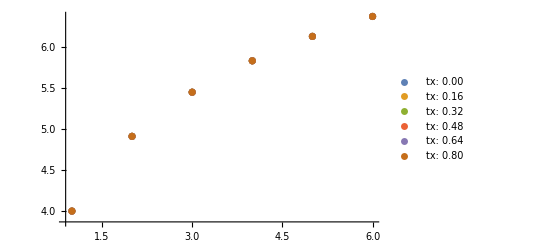

```mathematica
ListPlot[
Table[Accumulate[integratedTz[[i]]], {i, Length[tzlist]}], PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  tzlist], PlotRange->All]
```

```mathematica
If[terms=={0,0,1},thirdTermContrib = integratedTz];
```

```mathematica
If[terms=={0,1},secondTermContrib = integratedTz];
```

```mathematica
If[terms=={1,0},firstTermContrib=integratedTz];
```

NIntegrate::inumri: The integrand (2 (-0.68 kappa+√(1+kappa^2)) (HeavisideTheta[0.84 kappa]-HeavisideTheta[-0.16 kappa-Power[«2»]]))/((-1. kappa-√(1+Power[«2»]))^2 (-kappa+√(1+kappa^2))^2 (1+1/(-kappa+√Plus[«2»])^2))-(«1»)/(«1»)+«6»+(2 «1» («1»))/(«1»)-(2 («1») (-HeavisideTheta[-0.84 kappa]+HeavisideTheta[0.16 kappa+√(«1»)]))/((-1. kappa-√(1+Power[«2»]))^2 (-kappa+√(1+«1»))^2 (1+1/(-«5»+«1»)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-4.64782×10^14}}.

NIntegrate::inumri: The integrand «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.64782×10^14}}.

NIntegrate::inumri: The integrand (6 (0.32 kappa-√(2+kappa^2)+√(3+kappa^2)) (HeavisideTheta[-0.16 kappa+√(2+Power[«2»])]-HeavisideTheta[-0.16 kappa-Power[«2»]]))/((-√(2+Power[«2»])-√(3+Power[«2»]))^2 (-kappa+√(3+kappa^2))^2 (1+2/(Times[«2»]+«1»)^2) (1+3/(Times[«2»]+Power[«2»])^2))-(«1»)/(«1»)+«6»+«1»-(6 «1» (-HeavisideTheta[«1»]+HeavisideTheta[«1»+«1»]))/((-√(2+Power[«1»])-√(«1»))^2 («1»)^2 (1+2/(«1»)) (1+3/(«1»)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.64782×10^14}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
firstTermContrib/secondTermContrib //TableForm
```

NIntegrate::inumri: The integrand (2 (-0.68 kappa+√(1+kappa^2)) (HeavisideTheta[0.84 kappa]-HeavisideTheta[-0.16 kappa-Power[«2»]]))/((-1. kappa-√(1+Power[«2»]))^2 (-kappa+√(1+kappa^2))^2 (1+1/(-kappa+√Plus[«2»])^2))-(«1»)/(«1»)+«6»+(2 «1» («1»))/(«1»)-(2 («1») (-HeavisideTheta[-0.84 kappa]+HeavisideTheta[0.16 kappa+√(«1»)]))/((-1. kappa-√(1+Power[«2»]))^2 (-kappa+√(1+«1»))^2 (1+1/(-«5»+«1»)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,-4.64782×10^14}}.

NIntegrate::inumri: The integrand «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.64782×10^14}}.

NIntegrate::inumri: The integrand (6 (0.32 kappa-√(2+kappa^2)+√(3+kappa^2)) (HeavisideTheta[-0.16 kappa+√(2+Power[«2»])]-HeavisideTheta[-0.16 kappa-Power[«2»]]))/((-√(2+Power[«2»])-√(3+Power[«2»]))^2 (-kappa+√(3+kappa^2))^2 (1+2/(Times[«2»]+«1»)^2) (1+3/(Times[«2»]+Power[«2»])^2))-(«1»)/(«1»)+«6»+«1»-(6 «1» (-HeavisideTheta[«1»]+HeavisideTheta[«1»+«1»]))/((-√(2+Power[«1»])-√(«1»))^2 («1»)^2 (1+2/(«1»)) (1+3/(«1»)^2)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.64782×10^14}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

$Aborted

```mathematica
firstTermContrib +secondTermContrib //TableForm
```

8. | 1.81929 | 1.07535 | 0.765042 | 0.594064 | 0.485653
8. | 1.81929 | 1.07535 | 0.765042 | 0.594064 | 0.485653
8. | 1.81929 | 1.07535 | 0.765042 | 0.594064 | 0.485653
8. | 1.81929 | 1.07535 | 0.765042 | 0.594064 | 0.485653
8. | 1.81929 | 1.07535 | 0.765042 | 0.594064 | 0.485653
8. | 1.81929 | 1.07535 | 0.765042 | 0.594064 | 0.485653

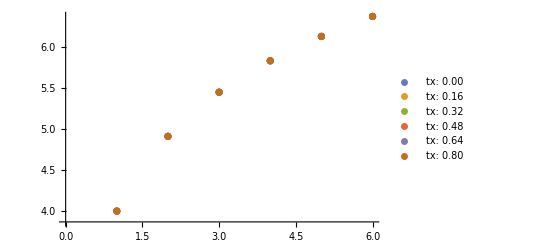

```mathematica
ListPlot[
Table[Accumulate[integratedTz[[i]]], {i, Length[tzlist]}], PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  tzlist]]
```

```mathematica
Table[
integratedTz[[i]]-(integratedTz[[i]][[-1]]-integratedTz[[1]][[-1]]),
{i, Length[tzlist]}
]
```

{{4.,0.909645,0.537675,0.382521,0.297032,0.242826},{4.,0.909645,0.537675,0.382521,0.297032,0.242826},{4.,0.909645,0.537675,0.382521,0.297032,0.242826},{4.,0.909645,0.537675,0.382521,0.297032,0.242826},{4.,0.909645,0.537675,0.382521,0.297032,0.242826},{4.,0.909645,0.537675,0.382521,0.297032,0.242826}}

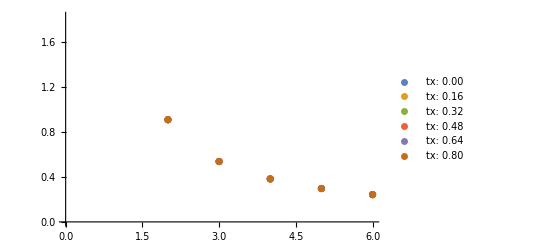

```mathematica
ListPlot[%, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  tzlist]]
```

## R & D mess

### Finding the anlytical contrib for tz>1

```mathematica
xi firstTerm[n]/.{m->1, n->2}
```

(4 (√(1+kappa^2)+√(2+kappa^2)) (HeavisideTheta[-√(1+kappa^2)-kappa tz]-HeavisideTheta[-√(2+kappa^2)-kappa tz]))/((√(1+kappa^2)-√(2+kappa^2))^2 (-kappa+√(2+kappa^2) s)^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (1+2/((-kappa+√(2+kappa^2) s)^2)))

```mathematica
FullSimplify[%/.s->1, Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

1/(2 √(2+3 kappa^2+kappa^4))(-kappa+2 √(1+kappa^2)+√(2+kappa^2)) (3+2 kappa^2+2 √(2+3 kappa^2+kappa^4)) (HeavisideTheta[-√(1+kappa^2)-kappa tz]-HeavisideTheta[-√(2+kappa^2)-kappa tz])

```mathematica
FullSimplify[%%/.s->-1, Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

((1-kappa/(√(1+kappa^2))) (kappa+√(1+kappa^2))^2 (√(1+kappa^2)+√(2+kappa^2)) (HeavisideTheta[-√(1+kappa^2)-kappa tz]-HeavisideTheta[-√(2+kappa^2)-kappa tz]))/((√(1+kappa^2)-√(2+kappa^2))^2 (2+kappa (kappa+√(2+kappa^2))))

```mathematica
FullSimplify[%%%, Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

((√(1+kappa^2)+√(2+kappa^2)) (3+2 kappa^2+2 √(2+3 kappa^2+kappa^4)) (kappa-√(1+kappa^2) s)^2 (HeavisideTheta[-√(1+kappa^2)-kappa tz]-HeavisideTheta[-√(2+kappa^2)-kappa tz]))/((1+kappa^2-kappa √(1+kappa^2) s) (2+kappa^2-kappa √(2+kappa^2) s))

```mathematica
Integrate[
((1-kappa/(√(1+kappa^2))) (kappa+√(1+kappa^2))^2 (√(1+kappa^2)+√(2+kappa^2)) )/((√(1+kappa^2)-√(2+kappa^2))^2 (2+kappa (kappa+√(2+kappa^2)))),
{kappa, -√(2/(-1+tz^2)),-√(1/(-1+tz^2))},
Assumptions->{{tz,s}∈Reals, s^2==1, tz>1}
]
```

$Aborted

```mathematica
NIntegrate[
((1-kappa/(√(1+kappa^2))) (kappa+√(1+kappa^2))^2 (√(1+kappa^2)+√(2+kappa^2)) )/((√(1+kappa^2)-√(2+kappa^2))^2 (2+kappa (kappa+√(2+kappa^2)))) ,
{kappa, -√(2/(-1+tz^2)),-√(1/(-1+tz^2))}
]/.tz->1.01
```

NIntegrate::nlim: kappa = -1.41421 √(1/(-1.+tz^2)) is not a valid limit of integration.

100.883

```mathematica
(1+s tz)/(s(tz^2-1))/.ssub/.tz->1.01
```

{100.,0.497512}

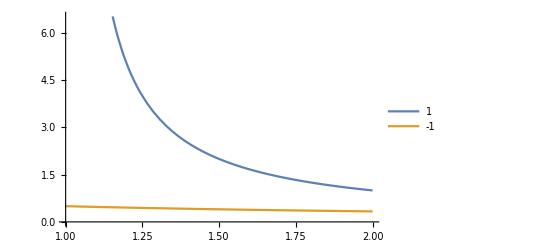

```mathematica
Plot[Evaluate[(1+s tz)/(s(tz^2-1))/.ssub], {tz, 1,2}, PlotLegends->(s/.ssub)]
```

```mathematica
Integrate[
(√(1+kappa^2)-kappa s+2 kappa tz)/(1+kappa^2+kappa √(1+kappa^2) s),
{kappa, -√(1/(-1+tz^2)),0},
Assumptions->{{tz,s}∈Reals, s^2==1, tz>1}
]
```

(-1+tz ArcCsch[√(-1+tz^2)])/s

```mathematica
Reduce[(s (kappa-kappa tz))(-√(1+kappa^2)-kappa s tz)<0,kappa]
```

(s<-1&&((tz<1/s&&-√(1/(-1+s^2 tz^2))<kappa<0)||(1/s≤tz≤-1/s&&kappa<0)||(-1/s<tz<1&&(kappa<0||kappa>√(1/(-1+s^2 tz^2))))||(tz>1&&0<kappa<√(1/(-1+s^2 tz^2)))))||(-1≤s<0&&((tz<1/s&&-√(1/(-1+s^2 tz^2))<kappa<0)||(1/s≤tz<1&&kappa<0)||(1<tz≤-1/s&&kappa>0)||(tz>-1/s&&0<kappa<√(1/(-1+s^2 tz^2)))))||(0<s≤1&&((tz<-1/s&&0<kappa<√(1/(-1+s^2 tz^2)))||(-1/s≤tz<1&&kappa>0)||(1<tz≤1/s&&kappa<0)||(tz>1/s&&-√(1/(-1+s^2 tz^2))<kappa<0)))||(s>1&&((tz<-1/s&&0<kappa<√(1/(-1+s^2 tz^2)))||(-1/s≤tz≤1/s&&kappa>0)||(1/s<tz<1&&(kappa<-√(1/(-1+s^2 tz^2))||kappa>0))||(tz>1&&-√(1/(-1+s^2 tz^2))<kappa<0)))

```mathematica
FullSimplify[(√(1+kappa^2)-kappa s+2 kappa tz)/(1+kappa^2+kappa √(1+kappa^2) s), Assumptions->{{kappa, s,tz}∈Reals, s^2==1}]
```

(√(1+kappa^2)-kappa s+2 kappa tz)/(1+kappa^2+kappa √(1+kappa^2) s)

```mathematica
Integrate[
(√(1+kappa^2)-kappa s+2 kappa tz)/(1+kappa^2+kappa √(1+kappa^2) s),
{kappa, -√(1/(-1+tz^2)),0},
Assumptions->{{tz,s}∈Reals, s^2==1, tz>1}
]
```

(-1+tz ArcCsch[√(-1+tz^2)])/s

```mathematica
Limit[(-1+tz ArcCsch[√(-1+tz^2)])/s/.s->1, tz->0]
```

-1

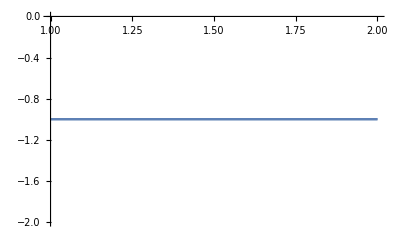

```mathematica
Plot[
%/.ssub,
{tz, 1,2}
]
```

```mathematica
kernel[n]/.{m->0,n->-1}
```

(2 (-√(1+kappa^2)-kappa tz+kappa (-s+tz)) (HeavisideTheta[-kappa (-s+tz)]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2) s)^2 (1+1/((-kappa-√(1+kappa^2) s)^2)) (√(1+kappa^2)-kappa tz+kappa (-s+tz))^2)

```mathematica
FullSimplify[%, Assumptions->{{s, tz, kappa}∈Reals, s^2==1}]
```

((√(1+kappa^2)+kappa s) (-HeavisideTheta[kappa (s-tz)]+HeavisideTheta[√(1+kappa^2)-kappa tz]))/(1+kappa^2-kappa √(1+kappa^2) s)

```mathematica
Reduce[(kappa (s-tz))(√(1+kappa^2)-kappa tz)<0,kappa]
```

(s<-1&&((tz<s&&-√(1/(-1+tz^2))<kappa<0)||(s<tz<-1&&(kappa<-√(1/(-1+tz^2))||kappa>0))||(-1≤tz≤1&&kappa>0)||(tz>1&&0<kappa<√(1/(-1+tz^2)))))||(-1≤s≤1&&((tz<-1&&-√(1/(-1+tz^2))<kappa<0)||(-1≤tz<s&&kappa<0)||(s<tz≤1&&kappa>0)||(tz>1&&0<kappa<√(1/(-1+tz^2)))))||(s>1&&((tz<-1&&-√(1/(-1+tz^2))<kappa<0)||(-1≤tz≤1&&kappa<0)||(1<tz<s&&(kappa<0||kappa>√(1/(-1+tz^2))))||(tz>s&&0<kappa<√(1/(-1+tz^2)))))

```mathematica
FullSimplify[(√(1+kappa^2)+kappa (s-2 tz))/(1+kappa^2-kappa √(1+kappa^2) s), Assumptions->{{kappa, s,tz}∈Reals, s^2==1}]
```

(√(1+kappa^2)+kappa s-2 kappa tz)/(1+kappa^2-kappa √(1+kappa^2) s)

```mathematica
Integrate[
(√(1+kappa^2)+kappa s-2 kappa tz)/(1+kappa^2-kappa √(1+kappa^2) s),
{kappa, 0,√(1/(-1+tz^2))},
Assumptions->{{tz,s}∈Reals, s^2==1, tz>1}
]
```

(-1+tz ArcCsch[√(-1+tz^2)])/s

### Other mess

```mathematica
mntable[[1]]
```

(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa (1-tz)]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa (1-tz)]-HeavisideTheta[√(1+kappa^2)+kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)

```mathematica
(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[kappa ]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[kappa ]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa ]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa ]-HeavisideTheta[√(1+kappa^2)+kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)
```

(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[kappa]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[kappa]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa]-HeavisideTheta[√(1+kappa^2)+kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)

```mathematica
FullSimplify[(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)+(2 (√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa (1-tz)]-HeavisideTheta[-√(1+kappa^2)+kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (1-tz)+kappa tz)^2)+(2 (-√(1+kappa^2)+kappa (1-tz)-kappa tz) (HeavisideTheta[-kappa (1-tz)]-HeavisideTheta[√(1+kappa^2)+kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (1-tz)+kappa tz)^2),
Assumptions->{{kappa, tz} ∈Reals, 0<=tz<1}
]
```

-1/(1+kappa^2)(2 √(1+kappa^2) (-1+2 kappa^2 (-1+tz))+4 (kappa+kappa^3) (-1+tz) (HeavisideTheta[kappa (-1+tz)]-HeavisideTheta[kappa-kappa tz]))

```mathematica
NIntegrate[-1/(1+kappa^2)(2 √(1+kappa^2) (-1+2 kappa^2 (-1+tz))+4 (kappa+kappa^3) (-1+tz) (HeavisideTheta[kappa (-1+tz)]-HeavisideTheta[kappa-kappa tz]))/.tz->0.16, {kappa, -Infinity, Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-6.00789×10^14}. NIntegrate obtained 3.91737×10^18 and 3.91744×10^18 for the integral and error estimates.

3.91737×10^18

```mathematica
FullSimplify[mntableINTRA[[2]], Assumptions->{tz,kappa}∈Reals]
```

1/(2+3 kappa^2+kappa^4)(6+4 √(2+3 kappa^2+kappa^4)+3 kappa^2 (3+kappa^2+√(2+3 kappa^2+kappa^4))) ((√(1+kappa^2)+√(2+kappa^2)+2 kappa tz) HeavisideTheta[-√(1+kappa^2)-kappa tz]-(√(1+kappa^2)+√(2+kappa^2)-2 kappa tz) HeavisideTheta[√(1+kappa^2)-kappa tz]-√(1+kappa^2) HeavisideTheta[-√(2+kappa^2)-kappa tz]-√(2+kappa^2) HeavisideTheta[-√(2+kappa^2)-kappa tz]+√(1+kappa^2) HeavisideTheta[√(2+kappa^2)-kappa tz]+√(2+kappa^2) HeavisideTheta[√(2+kappa^2)-kappa tz]-2 kappa tz (HeavisideTheta[-√(2+kappa^2)-kappa tz]+HeavisideTheta[√(2+kappa^2)-kappa tz]))

```mathematica
(√(1+kappa^2)+√(2+kappa^2)+2 kappa tz) (HeavisideTheta[-√(1+kappa^2)-kappa tz]- HeavisideTheta[-√(2+kappa^2)-kappa tz])-(√(1+kappa^2)+√(2+kappa^2)-2 kappa tz)( HeavisideTheta[√(1+kappa^2)-kappa tz]+HeavisideTheta[√(2+kappa^2)-kappa tz])
```

```mathematica
Integrate[
((4+3 kappa^2+3 √(2+3 kappa^2+kappa^4)) (√(1+kappa^2)+√(2+kappa^2)-2 kappa tz))/(√(2+3 kappa^2+kappa^4)),
{kappa, 1/(√(-1+tz^2)),Sqrt[2]/(√(-1+tz^2))},Assumptions->{{kappa,tz}∈Reals,tz>1}
]
```

1/4 (-12 √2 √(1+tz^2)+12 √(-1+2 tz^2)-16 ArcSinh[1/(√2 √(-1+tz^2))]+16 ArcSinh[(√2)/(√(-1+tz^2))]-tz Log[1+3 tz^2-2 √2 tz √(1+tz^2)]+tz Log[1+3 tz^2+2 √2 tz √(1+tz^2)]+tz Log[-1+3 tz^2-2 tz √(-1+2 tz^2)]-tz Log[-1+3 tz^2+2 tz √(-1+2 tz^2)])

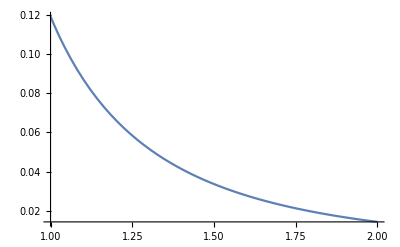

```mathematica
Plot[1/4 (-12 √2 √(1+tz^2)+12 √(-1+2 tz^2)-16 ArcSinh[1/(√2 √(-1+tz^2))]+16 ArcSinh[(√2)/(√(-1+tz^2))]-tz Log[1+3 tz^2-2 √2 tz √(1+tz^2)]+tz Log[1+3 tz^2+2 √2 tz √(1+tz^2)]+tz Log[-1+3 tz^2-2 tz √(-1+2 tz^2)]-tz Log[-1+3 tz^2+2 tz √(-1+2 tz^2)]), {tz, 1,2}]
```

```mathematica
FullSimplify[1/(2+3 kappa^2+kappa^4)(6+4 √(2+3 kappa^2+kappa^4)+3 kappa^2 (3+kappa^2+√(2+3 kappa^2+kappa^4))) (√(1+kappa^2)+√(2+kappa^2)-2 kappa tz), Assumptions->{kappa,tz}∈Reals]
```

((4+3 kappa^2+3 √(2+3 kappa^2+kappa^4)) (√(1+kappa^2)+√(2+kappa^2)-2 kappa tz))/(√(2+3 kappa^2+kappa^4))

```mathematica
Manipulate[
Plot[
{(HeavisideTheta[-√(1+kappa^2)-kappa tz]- HeavisideTheta[-√(2+kappa^2)-kappa tz]), -HeavisideTheta[√(1+kappa^2)-kappa tz]+HeavisideTheta[√(2+kappa^2)-kappa tz] },
{kappa,-4,4},PlotLegends->Automatic
],
{tz,0,2}]
```

```mathematica
Manipulate[
Plot[(√(1+kappa^2)+√(2+kappa^2)+2 kappa tz) HeavisideTheta[-√(1+kappa^2)-kappa tz]-(√(1+kappa^2)+√(2+kappa^2)-2 kappa tz) HeavisideTheta[√(1+kappa^2)-kappa tz]-√(1+kappa^2) HeavisideTheta[-√(2+kappa^2)-kappa tz]-√(2+kappa^2) HeavisideTheta[-√(2+kappa^2)-kappa tz]+√(1+kappa^2) HeavisideTheta[√(2+kappa^2)-kappa tz]+√(2+kappa^2) HeavisideTheta[√(2+kappa^2)-kappa tz]-2 kappa tz (HeavisideTheta[-√(2+kappa^2)-kappa tz]+HeavisideTheta[√(2+kappa^2)-kappa tz]), {kappa, -4,4}],
{tz, 0,2}]
```

```mathematica
(kernel[n]/.{m->1, n->2})/.s->-1
```

-((2 (2/((-kappa-√(1+kappa^2)) (-kappa-√(2+kappa^2))^2)+2/(-kappa-√(2+kappa^2))) (HeavisideTheta[-√(1+kappa^2)-kappa tz]-HeavisideTheta[-√(2+kappa^2)-kappa tz]))/((√(1+kappa^2)-√(2+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (1+2/((-kappa-√(2+kappa^2))^2))))

```mathematica
Reduce[(-√(1+kappa^2)-kappa tz)(-√(2+kappa^2)-kappa tz)<0]
```

(tz<-1&&√(1/(-1+tz^2))<kappa<√2 √(1/(-1+tz^2)))||(tz>1&&-√2 √(1/(-1+tz^2))<kappa<-√(1/(-1+tz^2)))

```mathematica
NIntegrate[
(4 (-kappa+√(2+kappa^2)+1/(-kappa+√(1+kappa^2))))/((kappa-√(2+kappa^2))^2 (√(1+kappa^2)-√(2+kappa^2))^2 (1+1/((kappa-√(1+kappa^2))^2)) (1+2/((kappa-√(2+kappa^2))^2))),
{kappa, -√2 √(1/(-1+tz^2)),-√(1/(-1+tz^2))}
]/.tz->1.1
```

NIntegrate::nlim: kappa = -1.41421 √(1/(-1.+tz^2)) is not a valid limit of integration.

20.3825

```mathematica
(kernel[n]/.{m->0, n->1})/.s->1
```

(2 (√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[-√(1+kappa^2)-kappa tz]))/((-kappa+√(1+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2))^2)) (-√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)

```mathematica
(kernel[n]/.{m->0, n->1})/.s->1
```

(2 (-√(1+kappa^2)+kappa (-1+tz)+kappa tz) (HeavisideTheta[-kappa (-1+tz)]-HeavisideTheta[√(1+kappa^2)-kappa tz]))/((-kappa-√(1+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2))^2)) (√(1+kappa^2)+kappa (-1+tz)-kappa tz)^2)

```mathematica
NIntegrate[funcs[[1]], {kappa,-Infinity, Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in kappa near {kappa} = {-2.43643}. NIntegrate obtained 12.5116 and 0.01487 for the integral and error estimates.

12.5116

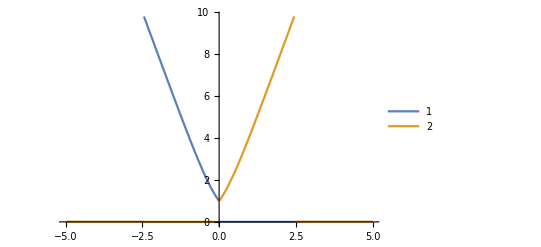

```mathematica
funcs={(kernel[n]/.{m->0, n->1}),(kernel[n]/.{m->0, n->-1})}/.{s->1,tz->1.08};
Plot[
funcs,
{kappa, -5,5},
PlotRange->All,
PlotLegends->Automatic
]
```

```mathematica
Manipulate[
Plot[mntableINTRA[[2]] +mntable[[2]]0/.tz->x, {kappa, -4,4}],
{x, -1.2,1.2}
]
```

```mathematica
(ϵ[m]-ϵ[n])/.ssub/.{m->-1, n->2}/.kappa->0//N
```

{-2.41421,-2.41421}

```mathematica
(ϵ[m]+ϵ[n])/.s->1/.{{m->1, n->2},{m->-1, n->-2, kappa->-kappa}}
```

{√(1+kappa^2)+√(2+kappa^2)+2 kappa tz,-√(1+kappa^2)-√(2+kappa^2)-2 kappa tz}

```mathematica
Manipulate[
Plot[ alpha[n]xi (ϵ[m]+ϵ[n])/.s->1/.{{m->1, n->2},{m->-1, n->-2}}/.tz->x, {kappa, -4,4}],
{x, -1.2,1.2}
]
```

```mathematica
s
```

```mathematica
xi (ϵ[m]+ϵ[n])alpha[n]^2 /.{{m->1, n->-2},{m->-1, n->2}}/.tz->0
```

{(4 (√(1+kappa^2)-√(2+kappa^2)) (HeavisideTheta[-√(1+kappa^2)]-HeavisideTheta[√(2+kappa^2)]))/((√(1+kappa^2)+√(2+kappa^2))^2 (-kappa-√(2+kappa^2) s)^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (1+2/((-kappa-√(2+kappa^2) s)^2))),(4 (-√(1+kappa^2)+√(2+kappa^2)) (HeavisideTheta[√(1+kappa^2)]-HeavisideTheta[-√(2+kappa^2)]))/((-√(1+kappa^2)-√(2+kappa^2))^2 (-kappa+√(2+kappa^2) s)^2 (1+1/((-kappa-√(1+kappa^2) s)^2)) (1+2/((-kappa+√(2+kappa^2) s)^2)))}

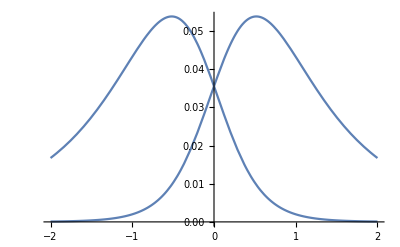

```mathematica
Plot[%955/.s->1, {kappa, -2, 2}]
```

```mathematica
xi (Sqrt[Abs[n]] alpha[n] + Sqrt[Abs[n]-1] alpha[m] alpha[n]^2)/.{{m->1, n->-2},{m->-1, n->2}}/.tz->0;
```

```mathematica
alpha[-2]
```

-(√2)/(-kappa-√(2+kappa^2) s)

```mathematica
xi/.{m->1,n->-2}
```

(2 (HeavisideTheta[-√(1+kappa^2)-kappa tz]-HeavisideTheta[√(2+kappa^2)-kappa tz]))/((√(1+kappa^2)+√(2+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (1+2/((-kappa-√(2+kappa^2) s)^2)))

```mathematica
Manipulate[
Plot[
Table[ϵ[n], {n, -4, 4}]/.s->y/.tz->x,
{kappa, -4, 4},
PlotRange->{-3,3}
],
{x, -1.2,1.2},
{y, -1,1,2}
]
```

```mathematica
Total[xi firstTerm[n]/.ssub]/.{m->1, n->-2}/.tz->0.8//Simplify
```

1/((√(1+kappa^2)+√(2+kappa^2))^2)4 (-((0.25 (kappa-1. √(1+kappa^2))^2 (-1.6 kappa-1. √(1+kappa^2)+√(2+kappa^2)) (HeavisideTheta[-0.8 kappa-1. √(1+kappa^2)]-1. HeavisideTheta[-0.8 kappa+√(2+kappa^2)]))/((1.+kappa^2-1. kappa √(1+kappa^2)) (2.+kappa^2+kappa √(2+kappa^2))))+(0.25 (kappa+√(1+kappa^2))^2 (-1.6 kappa+√(1+kappa^2)-1. √(2+kappa^2)) (HeavisideTheta[0.8 kappa-1. √(1+kappa^2)]-1. HeavisideTheta[0.8 kappa+√(2+kappa^2)]))/((1.+kappa^2+kappa √(1+kappa^2)) (2.+kappa^2-1. kappa √(2+kappa^2))))

```mathematica
Total[xi secondTerm/.ssub]/.{m->1, n->-2}/.tz->0.8//Simplify
```

1/((√(1+kappa^2)+√(2+kappa^2))^2)(-(((-kappa+√(1+kappa^2)) (-1-kappa^2+√(1+kappa^2) √(2+kappa^2)+kappa (√(1+kappa^2)-√(2+kappa^2))) (HeavisideTheta[-0.8 kappa-1. √(1+kappa^2)]-HeavisideTheta[-0.8 kappa+√(2+kappa^2)]))/((-1-kappa^2+kappa √(1+kappa^2)) (2+kappa^2+kappa √(2+kappa^2))))+((kappa+√(1+kappa^2)) (1+kappa^2-√(1+kappa^2) √(2+kappa^2)+kappa (√(1+kappa^2)-√(2+kappa^2))) (HeavisideTheta[0.8 kappa-1. √(1+kappa^2)]-HeavisideTheta[0.8 kappa+√(2+kappa^2)]))/((1+kappa^2+kappa √(1+kappa^2)) (2+kappa^2-kappa √(2+kappa^2))))

```mathematica
Total[xi secondTerm/.ssub]/.{m->-2, n->-3}/.tz->2//Simplify
```

1/((√(2+kappa^2)-√(3+kappa^2))^2)2 ((3 (kappa+√(2+kappa^2)) (2+kappa^2+√(2+kappa^2) √(3+kappa^2)+kappa (√(2+kappa^2)+√(3+kappa^2))) (HeavisideTheta[-2 kappa+√(2+kappa^2)]-HeavisideTheta[-2 kappa+√(3+kappa^2)]))/(4 (2+kappa^2+kappa √(2+kappa^2)) (3+kappa^2+kappa √(3+kappa^2)))+(3 (kappa-√(3+kappa^2)+2/(kappa-√(2+kappa^2))) (HeavisideTheta[2 kappa+√(2+kappa^2)]-HeavisideTheta[2 kappa+√(3+kappa^2)]))/((kappa-√(3+kappa^2))^2 (1+2/((kappa-√(2+kappa^2))^2)) (1+3/((kappa-√(3+kappa^2))^2))))

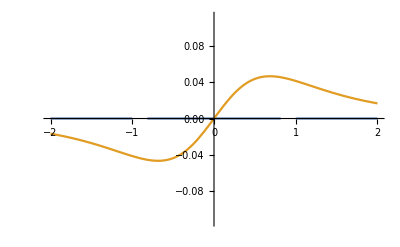

```mathematica
Plot[{%, %%}, {kappa, -2, 2}]
```

```mathematica
mntable=Table[
If[Abs[n]==Abs[m]+1,(xi firstTerm),0],
{m,-5,5}, {n,-10,10}
];
```

```mathematica
NIntegrate[mntable/.tz->0, {kappa, -Infinity, Infinity}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumr: The integrand (2 firstTerm (HeavisideTheta[√(5+kappa^2)]-HeavisideTheta[-√(6+Power[«2»])]))/((-√(5+kappa^2)-√(6+kappa^2))^2 (1+5/(-kappa-Power[«2»] s)^2) (1+6/(-kappa+Power[«2»] s)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand (2 firstTerm (HeavisideTheta[√(4+kappa^2)]-HeavisideTheta[-√(5+Power[«2»])]))/((-√(4+kappa^2)-√(5+kappa^2))^2 (1+4/(-kappa-Power[«2»] s)^2) (1+5/(-kappa+Power[«2»] s)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand (2 firstTerm (HeavisideTheta[√(3+kappa^2)]-HeavisideTheta[-√(4+Power[«2»])]))/((-√(3+kappa^2)-√(4+kappa^2))^2 (1+3/(-kappa-Power[«2»] s)^2) (1+4/(-kappa+Power[«2»] s)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(5+kappa^2)]-HeavisideTheta[-√(6+kappa^2)]))/((-√(5+kappa^2)-√(6+kappa^2))^2 (1+5/((-kappa-√(5+kappa^2) s)^2)) (1+6/((-kappa+√(6+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(4+kappa^2)]-HeavisideTheta[-√(5+kappa^2)]))/((-√(4+kappa^2)-√(5+kappa^2))^2 (1+4/((-kappa-√(4+kappa^2) s)^2)) (1+5/((-kappa+√(5+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(3+kappa^2)]-HeavisideTheta[-√(4+kappa^2)]))/((-√(3+kappa^2)-√(4+kappa^2))^2 (1+3/((-kappa-√(3+kappa^2) s)^2)) (1+4/((-kappa+√(4+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(2+kappa^2)]-HeavisideTheta[-√(3+kappa^2)]))/((-√(2+kappa^2)-√(3+kappa^2))^2 (1+2/((-kappa-√(2+kappa^2) s)^2)) (1+3/((-kappa+√(3+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[√(1+kappa^2)]-HeavisideTheta[-√(2+kappa^2)]))/((-√(1+kappa^2)-√(2+kappa^2))^2 (1+1/((-kappa-√(1+kappa^2) s)^2)) (1+2/((-kappa+√(2+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (-HeavisideTheta[√(1+kappa^2)]+HeavisideTheta[kappa s]))/((√(1+kappa^2)-kappa s)^2 (1+1/((-kappa-√(1+kappa^2) s)^2))),{kappa,-∞,∞}],0.,NIntegrate[(2 firstTerm (-HeavisideTheta[-√(1+kappa^2)]+HeavisideTheta[kappa s]))/((-√(1+kappa^2)-kappa s)^2 (1+1/((-kappa+√(1+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(1+kappa^2)]-HeavisideTheta[√(2+kappa^2)]))/((√(1+kappa^2)+√(2+kappa^2))^2 (1+1/((-kappa+√(1+kappa^2) s)^2)) (1+2/((-kappa-√(2+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(2+kappa^2)]-HeavisideTheta[√(3+kappa^2)]))/((√(2+kappa^2)+√(3+kappa^2))^2 (1+2/((-kappa+√(2+kappa^2) s)^2)) (1+3/((-kappa-√(3+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(3+kappa^2)]-HeavisideTheta[√(4+kappa^2)]))/((√(3+kappa^2)+√(4+kappa^2))^2 (1+3/((-kappa+√(3+kappa^2) s)^2)) (1+4/((-kappa-√(4+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(4+kappa^2)]-HeavisideTheta[√(5+kappa^2)]))/((√(4+kappa^2)+√(5+kappa^2))^2 (1+4/((-kappa+√(4+kappa^2) s)^2)) (1+5/((-kappa-√(5+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,NIntegrate[(2 firstTerm (HeavisideTheta[-√(5+kappa^2)]-HeavisideTheta[√(6+kappa^2)]))/((√(5+kappa^2)+√(6+kappa^2))^2 (1+5/((-kappa+√(5+kappa^2) s)^2)) (1+6/((-kappa-√(6+kappa^2) s)^2))),{kappa,-∞,∞}],0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

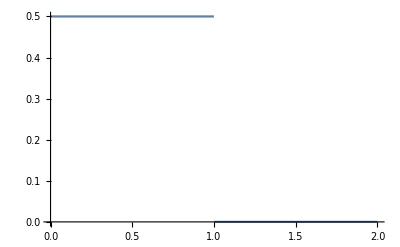

```mathematica
Plot[
Piecewise[{{1/2, tz<1}, {0, tz>1}}],
{tz,0,2}
]
```

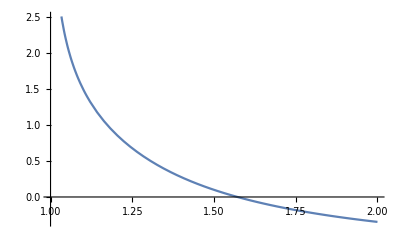

```mathematica
Plot[tz ArcCsch[tz^2-1]-1, {tz, 1,2}]
```